# Code Appendix

## Data Import

### Import

Import metadata such as the position of each of the feeding stations, water station and the corners of the paddock.

```mathematica
rawMetadata=Import["/Users/katjad/Documents/Github/SheepCapstone/Salt6_corners_food locations_collective decision making_March2019.csv"];
```

```mathematica
paddock=rawMetadata[[-4;;-1,-2;;-1]];
feeding=rawMetadata[[2;;11,-2;;-1]];
water=rawMetadata[[12,-2;;-1]];
```

Create a Graphics Boundary of the paddock

```mathematica
paddockRegion=BoundaryDiscretizeGraphics[Polygon[paddock]];metadataGraphic=Graphics[{LightBrown,Polygon[paddock],Darker[Green],Circle[#,30]&/@feeding,Thick,Darker[Blue],Circle[water,50]}];
```

Import the raw GPS data, so the X and Y coordinates as well as the time stamps and IDS.

```mathematica
rawXs=Import["/Users/katjad/Documents/Github/SheepCapstone/xs.csv"];
rawYs=Import["/Users/katjad/Documents/Github/SheepCapstone/ys.csv"];
rawIDs=Import["/Users/katjad/Documents/Github/SheepCapstone/ids.csv"];
rawTs=Import["/Users/katjad/Documents/Github/SheepCapstone/ts.csv"];
rawTsStart=Import["/Users/katjad/Documents/Github/SheepCapstone/period.start.idxs.csv"];
```

### Transform to full coordinates

The dataset has 51 sheep(+header) and 210352 time steps

Create two versions of the coordinates, one with missing data as Missing[] for more computational tasks and one with missing data as “Indeterminate” for mathematical tasks

```mathematica
rawCoordinates=Table[{rawXs[[x,y]],rawYs[[x,y]]},{x,2,52},{y,2,210352}]/."NA"->Missing[];
```

```mathematica
rawCoordinates2=rawCoordinates/.Missing[]->Indeterminate;
```

```mathematica
(*Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/ProcessedCoordinates/rawCoordinates.mx",rawCoordinates]*)
```

```mathematica
(*Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/ProcessedCoordinates/rawCoordinates2.mx",rawCoordinates2]*)
```

I exported the files so the formatting didn’t have to be re-done every time (more efficient) and commented out the export statements so they are not accidentally re-run.

```mathematica
rawCoordinates=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/ProcessedCoordinates/rawCoordinates.mx"];
```

```mathematica
rawCoordinates2=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/ProcessedCoordinates/rawCoordinates2.mx"];
```

### Split into 4 intervals

Separate into the four time periods of consecutive data

```mathematica
separatedTs=Rest[Split[rawTs[[All,2]],#2-#1<7&]];
```

```mathematica
splitSequences = Prepend[Accumulate[Length/@separatedTs],0];
```

Again, generating the rawCoordinates and rawCoordinates2 and exporting.

```mathematica
splitRawCoordinates=BlockMap[rawCoordinates[[All,#[[1]]+1;;#[[2]]]]&,splitSequences,2,1];
```

```mathematica
splitRawCoordinates2=splitRawCoordinates/.Missing[]->Indeterminate;
```

Export

```mathematica
(*Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/ProcessedCoordinates/splitRawCoordinates.mx",splitRawCoordinates]*)
```

```mathematica
(*Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/ProcessedCoordinates/splitRawCoordinates2.mx",splitRawCoordinates2]*)
```

Import

```mathematica
splitRawCoordinates=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/ProcessedCoordinates/splitRawCoordinates.mx"];
```

```mathematica
splitRawCoordinates2=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/ProcessedCoordinates/splitRawCoordinates2.mx"];
```

This yields four datasets with varying lengths.

```mathematica
Length[#[[1]]]&/@splitRawCoordinates
```

{53417,51685,52387,52862}

## Traditional DBSCAN and Clustering

### Distribution of distances

(To determine common distances)

#### Individual Sheep

Function to determine the distance between sheep a and b

```mathematica
distances[a_,b_]:=Sqrt[Total[(rawCoordinates2[[a]] - rawCoordinates2[[b]])^2,{2}]]
```

Running this on two sheep will yield the distance they are from each other at each time step

Creates a function that for a given sheep and time finds all other sheep within a specified radius

```mathematica
SingleSheepWithinRadius[radius_,sheep_,time_]:=
If[rawCoordinates[[sheep,time]]==={Missing[],Missing[]},
Missing[],Nearest[DeleteMissing[MapIndexed[#1->#2[[1]]&,rawCoordinates[[All,time]]],1,3],rawCoordinates[[sheep,time]],{All,radius}]]
```

At step 3000, sheep 7 has 3 other sheep with it in less than 50m radius

```mathematica
SingleSheepWithinRadius[50,7,3000]
```

{7,49,12,32}

This allows us to

```mathematica
sheep1herdsize=With[{herd=SingleSheepWithinRadius[100,1,#]},If[MissingQ[herd],Missing[],Length[herd]]]&/@Range[Length[rawCoordinates[[4]]]];
```

24.4138

22

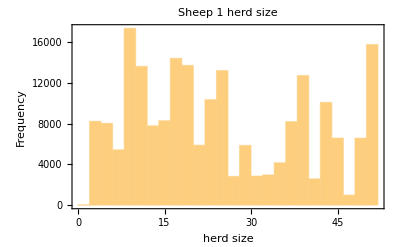

```mathematica
Mean[DeleteMissing[sheep1herdsize]]//N
Median[DeleteMissing[sheep1herdsize]]
Histogram[sheep1herdsize,PlotLabel->"Sheep 1 herd size",Frame->True,FrameLabel->{"herd size","Frequency"}]
ListLinePlot[sheep1herdsize,PlotLabel->"Sheep 1 herd size over time",Frame->True,FrameLabel->{"time","herd size"}]
```

#### Mean over all sheep

Set data Directory to export data to

```mathematica
dataDirectory="/Users/katjad/Documents/Github/SheepCapstone/MXs/DistanceData";
```

Create a function that gets the distances for a pair of sheep and exports the list as an .mx file.

```mathematica
exportDistance[a_,b_]:=
Module[{distance,name},
distance=distances[a,b];
name=StringJoin[ToString[a],"and",ToString[b],".mx"];
Export[FileNameJoin[{dataDirectory,name}],distance]]
```

Generate a list of all the names of the files that were exported.

```mathematica
PairNames=Table[StringJoin[ToString[a],"and",ToString[b],".mx"],{a,1,Length[rawCoordinates2]},{b,a+1,Length[rawCoordinates2]}];
```

Import the data one by one and find the mean and median of each

```mathematica
Module[{currentPairData,data},
data=Table[
currentPairData=DeleteCases[Import[FileNameJoin[{dataDirectory,name}]],Indeterminate];
{Median[currentPairData],Mean[currentPairData]},
{name,Flatten[PairNames]}];
medians=data[[All,1]];
means=data[[All,2]];]
Export[FileNameJoin[{dataDirectory,"medians.mx"}],medians];
Export[FileNameJoin[{dataDirectory,"means.mx"}],means];
```

Median::rectn: Rectangular array of real numbers is expected at position 1 in Median[{Missing[]}].

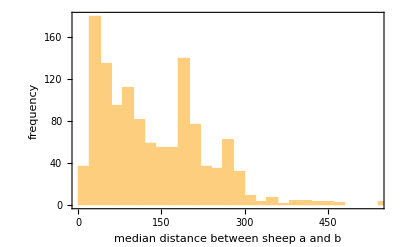

```mathematica
Histogram[medians,Frame->True,FrameLabel->{"median distance between sheep a and b","frequency"}]
```

#### Sampling from all pairs

Randomly sample two sheep and a times step and calculate their distance to each other to find the distribution on which to base the radius choice.

```mathematica
randomDistances=Select[Table[EuclideanDistance@@rawCoordinates2[[RandomInteger[{1,Length[rawCoordinates2]},2],RandomInteger[{1,Length[rawCoordinates2[[1]]]}]]],200000],#>0&];
```

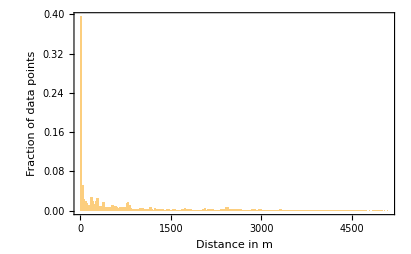

```mathematica
Histogram[randomDistances,{25},"Probability",Frame->True,FrameLabel->{"Distance in m","Fraction of data points"},PlotRange->All]
```

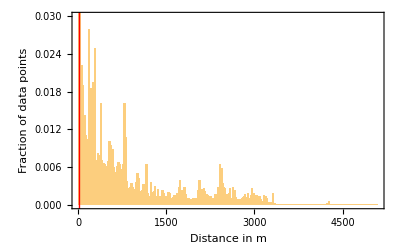

```mathematica
Histogram[randomDistances,{25},"Probability",Frame->True,FrameLabel->{"Distance in m","Fraction of data points"},PlotRange->{All,{0,0.03}},Epilog->{{Red,Thick,InfiniteLine[{{25,0},{25,1}}]}}]
```

```mathematica
Histogram[randomDistances,{50},Frame->True,FrameLabel->{"Distance","count"},ScalingFunctions->{"Log","Log"}]
```

```mathematica
feedingStationsDistances = DeleteCases[Flatten[DistanceMatrix[feeding]//N],0.];
```

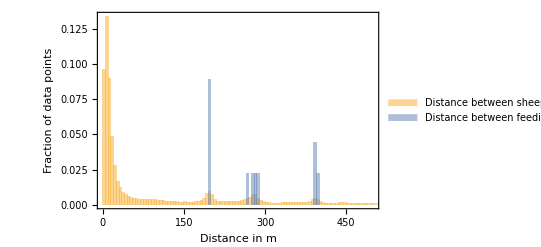

```mathematica
Histogram[{randomDistances,feedingStationsDistances},{5},"Probability",PlotRange->{{0,500},Automatic},Frame->True,FrameLabel-> {"Distance in m","Fraction of data points"},ChartLegends->{"Distance between sheep","Distance between feeding stations"}]
```

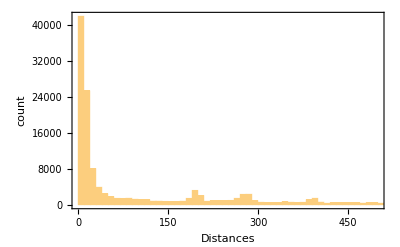

```mathematica
Histogram[randomDistances,{10},PlotRange->{{0,500},All},Frame->True,FrameLabel-> {"Distances","count"}]
```

#### Sampling from all pairs split by interval

Repeat for the split data set

```mathematica
splitRandomDistances=Function[coord,Select[Table[EuclideanDistance@@coord[[RandomInteger[{1,Length[coord]},2],RandomInteger[{1,Length[coord[[1]]]}]]],100000],#>0&]]/@splitRawCoordinates2;
```

```mathematica
Dimensions/@splitRandomDistances
```

{{92178},{86218},{93682},{93348}}

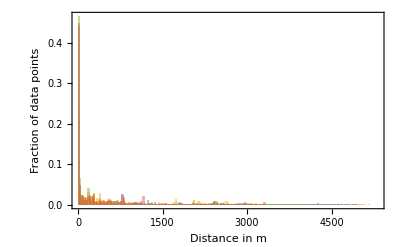

```mathematica
Histogram[splitRandomDistances,{25},"Probability",Frame->True,FrameLabel->{"Distance in m","Fraction of data points"},PlotRange->All]
```

All but the first one are very similar

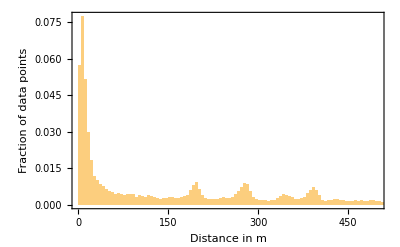
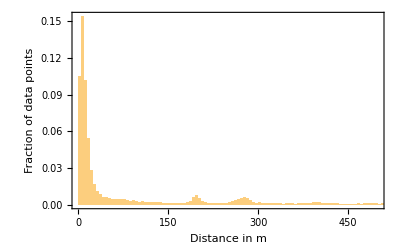
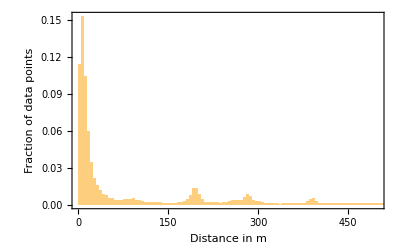
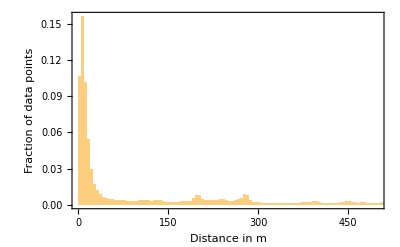

```mathematica
Histogram[splitRandomDistances[[#]],{5},"Probability",PlotRange->{{0,500},Automatic},Frame->True,FrameLabel-> {"Distance in m","Fraction of data points"}]&/@Range[4]
```

### Simple DBSCAN Implementation

A function that takes a time step and radius and returns a cluster

```mathematica
dbScanClusters[time_,radius_]:=
Module[{positions,rawClusters,outliers},
positions=DeleteMissing[MapIndexed[#1->#2[[1]]&,rawCoordinates[[All,time]]],1,3];
rawClusters=FindClusters[positions,Method->{"DBSCAN","NeighborhoodRadius"->radius,"DropAnomalousValues"->True},DistanceFunction->EuclideanDistance];
outliers=Complement[Values[positions],Flatten[rawClusters]];
Append[rawClusters,outliers]]
```

Plot example radii

```mathematica
dbScanComparison[time_]:=Column[{Show[metadataGraphic,Graphics[Style[Circle[#,50],Thin]&/@DeleteMissing[rawCoordinates[[All,time]],1,2],PlotRange->RegionBounds[paddockRegion]],PlotRange->{{580401.,582573.},{6.562693*^6,6.564282*^6}}],Show[metadataGraphic,ListPlot[FindClusters[DeleteMissing[rawCoordinates[[All,time]],1,2],Method->{"DBSCAN","NeighborhoodRadius"->10},DistanceFunction->EuclideanDistance],AspectRatio->Automatic],PlotRange->{{580401.,582573.},{6.562693*^6,6.564282*^6}}],Show[metadataGraphic,ListPlot[FindClusters[DeleteMissing[rawCoordinates[[All,time]],1,2],Method->{"DBSCAN","NeighborhoodRadius"->30},DistanceFunction->EuclideanDistance],AspectRatio->Automatic],PlotRange->{{580401.,582573.},{6.562693*^6,6.564282*^6}}],
Show[metadataGraphic,ListPlot[FindClusters[DeleteMissing[rawCoordinates[[All,time]],1,2],Method->{"DBSCAN","NeighborhoodRadius"->50},DistanceFunction->EuclideanDistance],AspectRatio->Automatic],PlotRange->{{580401.,582573.},{6.562693*^6,6.564282*^6}}]}]
```

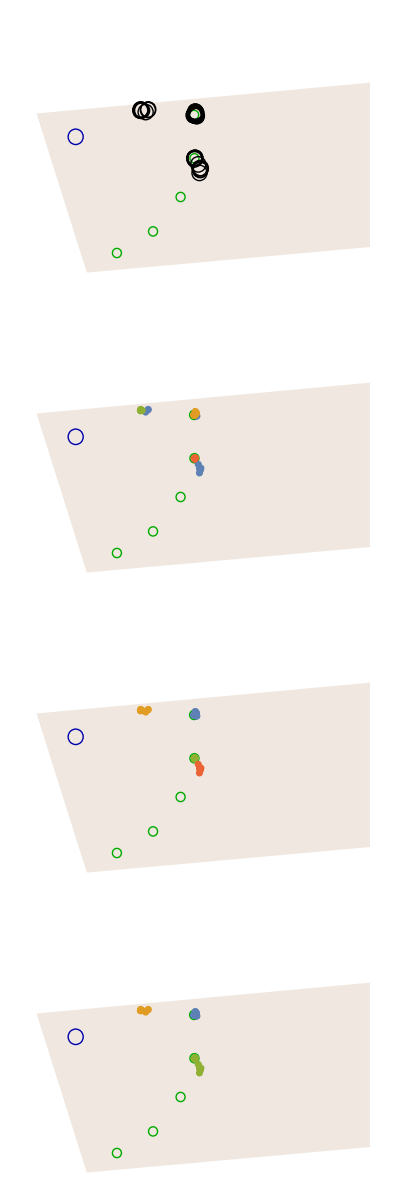

```mathematica
dbScanComparison[1000]
```

### Simple DBSCAN herds production

```mathematica
dbScanHerds5=Table[dbScanClusters[x,5],{x,1,Length[rawCoordinates[[1]]]}];
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds5.mx",dbScanHerds5];
```

```mathematica
dbScanHerds10=Table[dbScanClusters[x,10],{x,1,Length[rawCoordinates[[1]]]}];
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds10.mx",dbScanHerds10];
```

```mathematica
dbScanHerds20=Table[dbScanClusters[x,20],{x,1,Length[rawCoordinates[[1]]]}];
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds20.mx",dbScanHerds20];
```

```mathematica
dbScanHerds30=Table[dbScanClusters[x,30],{x,1,Length[rawCoordinates[[1]]]}];
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds30.mx",dbScanHerds30];
```

```mathematica
dbScanHerds50=Table[dbScanClusters[x,50],{x,1,Length[rawCoordinates[[1]]]}];
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds50.mx",dbScanHerds50];
```

```mathematica
dbScanHerds100=Table[dbScanClusters[x,100],{x,1,Length[rawCoordinates[[1]]]}];
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds100.mx",dbScanHerds100];
```

### Simple DBSCAN herds import

```mathematica
dbScanHerds5=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds5.mx"];
dbScanHerds10=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds5.mx"];
dbScanHerds20=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds20.mx"];
dbScanHerds30=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds30.mx"];
dbScanHerds50=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds50.mx"];
dbScanHerds100=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds100.mx"];
```

### Group Stability Simple DBSCAN

Split the single sheep into their own groups

```mathematica
dbScanHerds10LonelySheep=Join[Most[#],List/@Last[#]]&/@dbScanHerds10;
dbScanHerds30LonelySheep=Join[Most[#],List/@Last[#]]&/@dbScanHerds30;
dbScanHerds50LonelySheep=Join[Most[#],List/@Last[#]]&/@dbScanHerds50;
```

```mathematica
groupStability10=GroupBy[Catenate[MapIndexed[#1->First[#2]&,dbScanHerds10LonelySheep,{2}]],First->Last,Join];
```

```mathematica
groupStability30=GroupBy[Catenate[MapIndexed[#1->First[#2]&,dbScanHerds30LonelySheep,{2}]],First->Last,Join];
```

```mathematica
groupStability50=GroupBy[Catenate[MapIndexed[#1->First[#2]&,dbScanHerds50LonelySheep,{2}]],First->Last,Join];
```

### Graph generation Functions

Make the connections over time between the groups by setting a similarity threshold.

```mathematica
FindRulesFromTo[first_,second_,firstindex_,threshold_]:=
Module[{r},
r=Reap[
Table[If[(Length[c1]-Length[Complement[c1,c2]])/Length[c1]>threshold,
Sow[{c1,firstindex}->{c2,firstindex+1}]];If[(Length[c2]-Length[Complement[c2,c1]])/Length[c2]>threshold,
Sow[{c1,firstindex}->{c2,firstindex+1}]],{c1,first},{c2,second}]];
If[Flatten[DeleteCases[r,{Null},2]]==={},{},DeleteDuplicates[r[[2,1]]]
]]
```

```mathematica
FindFissionFusionGraph[tmin_,tmax_,threshold_,lonelySheep_]:=Graph[Catenate[Table[FindRulesFromTo[lonelySheep[[a]],lonelySheep[[a+1]],a,threshold],{a,tmin,tmax}]]];
```

```mathematica
g10=FindFissionFusionGraph[700,800,0.8,dbScanHerds10LonelySheep];
```

```mathematica
g30 =FindFissionFusionGraph[700,800,0.8,dbScanHerds30LonelySheep];
```

```mathematica
g50=FindFissionFusionGraph[700,800,0.8,dbScanHerds50LonelySheep];
```

### Plotting functions

Plot the functions with x representing time, y representing distance to the paddock corner, size representing group size, and color representing continuity

```mathematica
coloredGraph[g_,enlargingFactor_]:=HighlightGraph[Graph[g,VertexSize->(#->Length[First[#]]*enlargingFactor&/@VertexList[g]),VertexCoordinates->(#->{Last[#]*30,Mean[DeleteMissing[rawCoordinates[[#[[1]],Last[#],1]]]]-580401}&/@VertexList[g]),Frame->True,FrameTicks->True,EdgeShapeFunction->"Line",FrameLabel->{Style["Time in min since the start of data collection",Medium],Style["Horizontal distance to western paddock corner (m)",Medium]}],ConnectedComponents[UndirectedGraph[Subgraph[g,Select[VertexList[g],VertexDegree[g,#]===2&]]]]]
```

```mathematica
correctlabels[fig_]:=Show[fig,FrameTicks->ReplacePart[ MapAt[If[#[[2]]==="",#,ReplacePart[#,2->#[[1]]/300]]&,AbsoluteOptions[fig,FrameTicks][[1,2]],{1,All}],{{3},{4}}->None]]
```

### Examples (700-800)

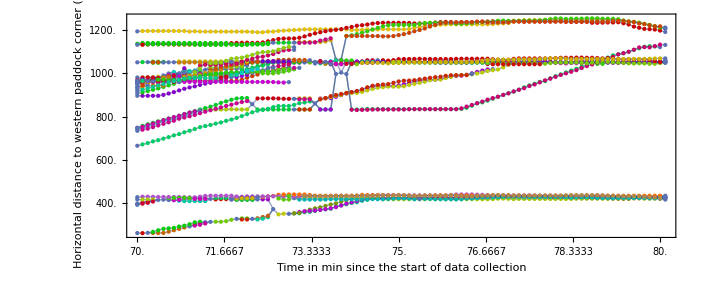

```mathematica
correctlabels[coloredGraph[g10,0.1]]
```

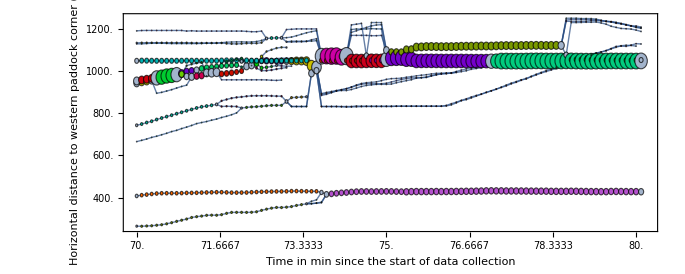

```mathematica
correctlabels[coloredGraph[g30,2000]]
```

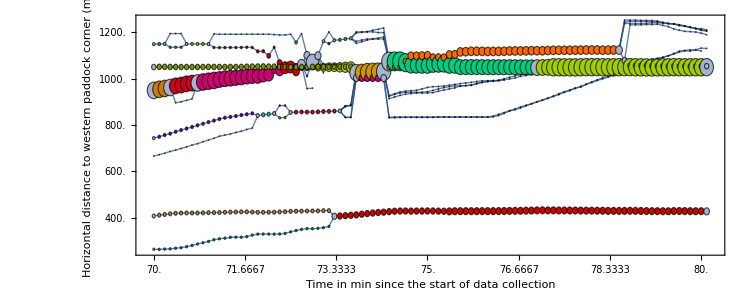

```mathematica
correctlabels[coloredGraph[g50,2000]]
```

#### Influence of Threshold

Run the same algorithm with a stricter threshold for group stability

```mathematica
gstrict=FindFissionFusionGraph[700,800,0.99,dbScanHerds50LonelySheep];
```

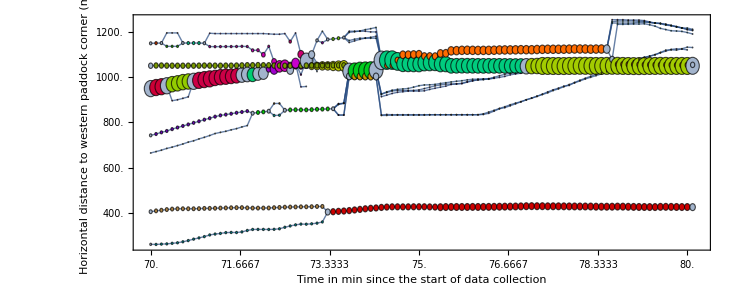

```mathematica
correctlabels[coloredGraph[gstrict,2000]]
```

```mathematica
animation=Animate[Show[metadataGraphic,Graphics[Circle[#,15]&/@DeleteMissing[rawCoordinates[[All,n]],1,2],PlotRange->RegionBounds[paddockRegion]],PlotRange->{{580401.,582573.},{6.562693*^6,6.564282*^6}}],{n,700,800,1}];
```

```mathematica
Export["/Users/katjad/Documents/Minerva/Capstone/Sheep/ActualMotionAnimation.mov",animation]
```

/Users/katjad/Documents/Minerva/Capstone/Sheep/ActualMotionAnimation.mov

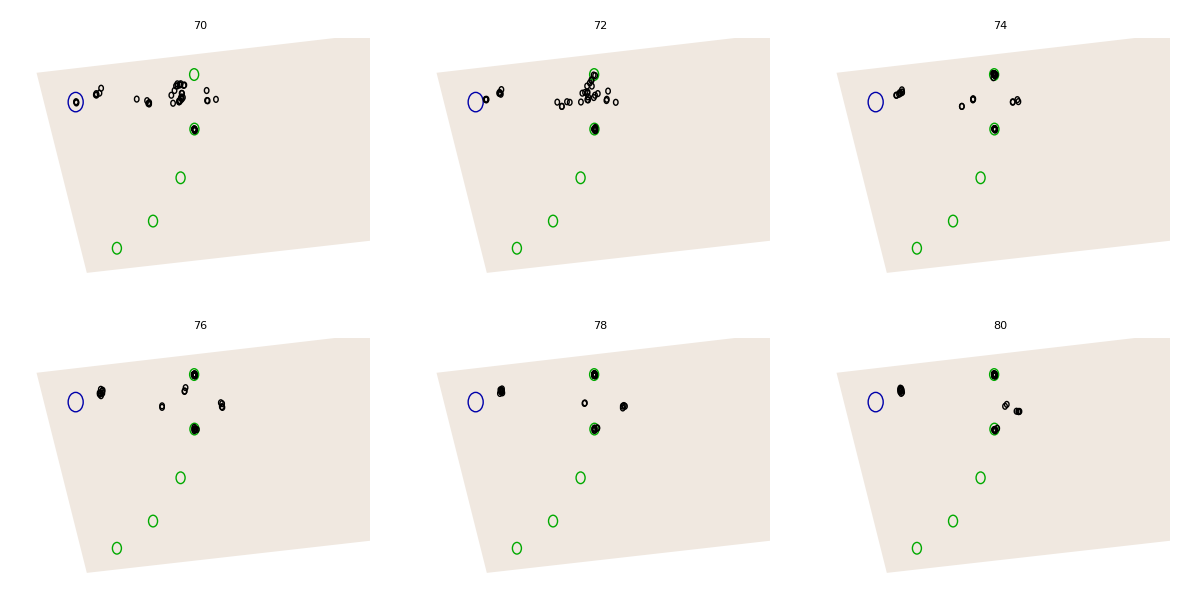

```mathematica
Grid[Partition[Table[Show[metadataGraphic,Graphics[Circle[#,15]&/@DeleteMissing[rawCoordinates[[All,n]],1,2],PlotRange->RegionBounds[paddockRegion]],PlotRange->{{580401.,582573.},{6.562693*^6,6.563882*^6}},PlotLabel->n/10],{n,700,800,20}],3]]
```

### Group Network some more examples

```mathematica
g50ExampleTwo=FindFissionFusionGraph[150000,150100,0.8,dbScanHerds50LonelySheep];
```

```mathematica
g50ExampleThree=FindFissionFusionGraph[100000,100100,0.8,dbScanHerds50LonelySheep];
```

```mathematica
Column[{coloredGraph[g50ExampleThree,100000],coloredGraph[g50ExampleTwo,100000]}]
```

-Graphics-

```mathematica
Animate[Show[metadataGraphic,Graphics[Circle[#,15]&/@DeleteMissing[rawCoordinates[[All,n]],1,2],PlotRange->RegionBounds[paddockRegion]]],{n,150000,150200,1}]
```

## Sticky DBSCAN

### Definition

New sticky DBSCAN modification that first determines connections by splitting in two radii...

```mathematica
determineConnections[pair_,{r1_,r2_}]:=
Module[{split,testList,final},
split=
Catenate/@Split[Split[pair,( #1≤r2&&#2≤r2||#1>r2&&#2>r2||#2===Indeterminate&)],With[{first=DeleteCases[#1,Indeterminate],second=DeleteCases[#2,Indeterminate]},first\[VectorLessEqual]r2&&second\[VectorLessEqual]r2||first\[VectorGreater]r2 &&second\[VectorGreater]r2]&];
testList=MemberQ[#,_?(Function[x,x<r1])]&/@split;
final =Catenate[MapIndexed[Table[testList[[First[#2]]],Length[#1]]&,split]]
]
```

... before putting it back together with a DBSCAN algorithm

```mathematica
symmetricalStickyDBSCAN[data_,{r1_,r2_},{tmin_,tmax_},rawCoordinates_]:=
Module[{cons,allEdges},
cons=Transpose[Catenate[Map[determineConnections[#,{r1,r2}]&,data[[All,All,tmin;;tmax]],{2}]]];
allEdges=UndirectedEdge@@@Catenate[MapIndexed[{#2[[1]],Total[#2]}&,data,{2}]];

MapIndexed[
With[{members=Flatten[Position[rawCoordinates[[All,tmin-1+First[#2]]],{__?NumericQ},{1},Heads->False]]},
ConnectedComponents[Graph[
(*pick vertexes*)
members,
(*pick connections*)
Select[Pick[allEdges,#1,True],FreeQ[Alternatives@@Complement[Range[Length[data]],members]]]]]]&,cons]]
```

### Tests

This is just good programming practice for complex pieces of code, so I tested whether different scenarios give the correct result

```mathematica
testData[testdist_]:=MapThread[Transpose[{##}]&,Function[{ps},MapIndexed[#1[[#2[[1]]+1;;]]&,DistanceMatrix[ps]]//N]/@testdist]
```

```mathematica
testcoordsFromDist[testdist_]:=List/@#&/@Transpose[testdist]
```

```mathematica
testDistDBSCAN[testdist_]:=symmetricalStickyDBSCAN[testData[testdist],{30,50},{1,Length[testdist]},testcoordsFromDist[testdist]]//Column
```

#### Expectation: sheep 4 moves from one group to the other group

```mathematica
testdistOneSheepMoves={{1,70,2,60},{2,80,3,6},{2,85,4,8}};
```

```mathematica
testDistDBSCAN[testdistOneSheepMoves]
```

{{1,3},{2,4}}
{{1,3,4},{2}}
{{1,3,4},{2}}

#### Expectation: Apart for the first 3 steps, together for 2, apart for 2

```mathematica
testdistInlargerRadius = {{1,40},{2,40},{2,70},{2,40},{1,20},{1,80},{2,50}};
```

```mathematica
testDistDBSCAN[testdistInlargerRadius]
```

{{1},{2}}
{{1},{2}}
{{1},{2}}
{{1,2}}
{{1,2}}
{{1},{2}}
{{1},{2}}

#### Expectation: One group for 2 steps, two groups for 2 steps

```mathematica
testDistConnected={{1,25,50},{1,35,70},{1,35,100},{1,35,70}};
```

```mathematica
testDistDBSCAN[testDistConnected]
```

{{1,2,3}}
{{1,2,3}}
{{2,1},{3}}
{{2,1},{3}}

#### Expectation: Together the first 4 steps, then apart for 1

```mathematica
testDistConnected={{1,25,50},{1,35,70},{1,35,Missing[]},{1,35,70},{1,70,Missing[]}};
```

```mathematica
testDistDBSCAN[testDistConnected]
```

{{1,2,3}}
{{1,2,3}}
{{1,2,3}}
{{1,2,3}}
{{1,3},{2}}

### Generate Data

```mathematica
DBSCAN30Sticky50LonelySheep=symmetricalStickyDBSCAN[allPairData,{30,50},{1,210351},rawCoordinates];
```

```mathematica
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/StickyDBScan/DBSCAN30Sticky50LonelySheep.mx",DBSCAN30Sticky50LonelySheep];
```

```mathematica
DBSCAN30Sticky50LonelySheep=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/StickyDBScan/DBSCAN30Sticky50LonelySheep.mx"];
```

### Plot

```mathematica
graph30Sticky50=FindFissionFusionGraph[700,800,0.8,DBSCAN30Sticky50LonelySheep];
```

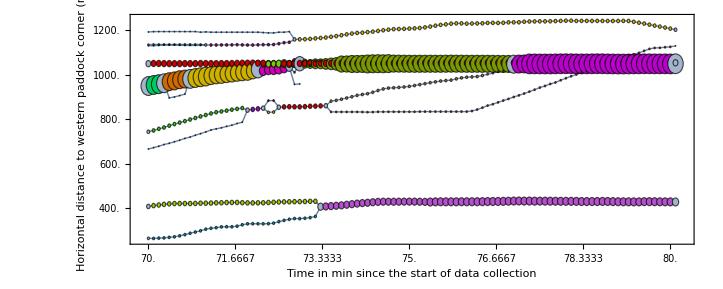

```mathematica
correctlabels[coloredGraph[graph30Sticky50,30]]
```

```mathematica
fullGraph30Sticky50=FindFissionFusionGraph[1,210350,0.8,DBSCAN30Sticky50LonelySheep];
```

$Aborted

```mathematica
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/StickyDBScan/fullGraph30Sticky50.mx",fullGraph30Sticky50]
```

/Users/katjad/Documents/Github/SheepCapstone/MXs/StickyDBScan/fullGraph30Sticky50.mx

## Fission-Fusion Analysis

### Locations

#### Absolute locations

Find fission and fusion events from the graph

```mathematica
fullGraph30Sticky50=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/StickyDBScan/fullGraph30Sticky50.mx"];
```

```mathematica
mergingEvents =Select[VertexList[fullGraph30Sticky50],VertexInDegree[fullGraph30Sticky50,#]≥2&];
```

```mathematica
splittingEvents =Select[VertexList[fullGraph30Sticky50],VertexOutDegree[fullGraph30Sticky50,#]≥ 2&];
```

Find the merging coordinates and plot them

```mathematica
mergingCoordinates =Mean[rawCoordinates[[#[[1]],#[[2]]]]]&/@mergingEvents;
```

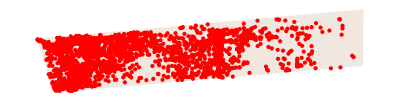

```mathematica
Show[metadataGraphic,Graphics[Style[Point[mergingCoordinates],Red]]]
```

Find the splitting coordinates and plot them

```mathematica
splittingCoordinates=Mean[rawCoordinates[[#[[1]],#[[2]]]]]&/@splittingEvents;
```

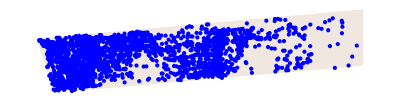

```mathematica
Show[metadataGraphic,Graphics[Style[Point[splittingCoordinates],Blue]]]
```

Find the distances to water and food and show the frequency of these events relative to that

```mathematica
mergingDistances=Nearest[pointsOfInterest->"Distance",mergingCoordinates][[All,1]];
```

```mathematica
splittingDistances=Nearest[pointsOfInterest->"Distance",splittingCoordinates][[All,1]];;
```

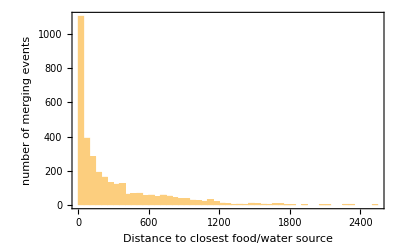

```mathematica
Histogram[mergingDistances,PlotRange->All,Frame->True,FrameLabel->{"Distance to closest food/water source","number of merging events"}]
```

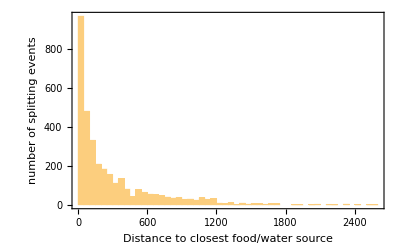

```mathematica
Histogram[splittingDistances,PlotRange->All,Frame->True,FrameLabel->{"Distance to closest food/water source","number of splitting events"}]
```

#### Normalized by density

Situate the events in a grid of 50 by 50 squares

```mathematica
allCoordinates=Mean[rawCoordinates[[#[[1]],#[[2]]]]]&/@VertexList[fullGraph30Sticky50];
```

```mathematica
splittingArray=BinCounts[splittingCoordinates,{580401,586573,50},{6.562693*^6,6.564282*^6,50}];
```

```mathematica
mergingArray=BinCounts[mergingCoordinates,{580401,586573,50},{6.562693*^6,6.564282*^6,50}];
```

```mathematica
allCoordinatesArray=BinCounts[allCoordinates,{580401,586573,50},{6.562693*^6,6.564282*^6,50}];
```

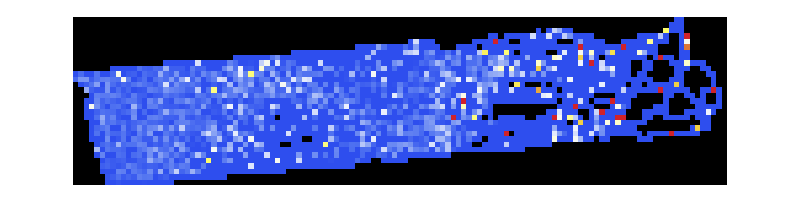

```mathematica
Row[{Show[{
metadataGraphic,Graphics[Raster[Map[If[#===Indeterminate,{0,0,0,0},Append[List@@ColorData["TemperatureMap"][#*10],0.8]]&,Transpose[Quiet[splittingArray/allCoordinatesArray]],{2}],Transpose[RegionBounds[paddockRegion]]]]
},ImageSize->800],BarLegend[{"TemperatureMap",{0,0.1}},LegendLabel->"Splitting event density"]}]
```

```mathematica
BarLegend[{"TemperatureMap",{0,0.1}}]
```

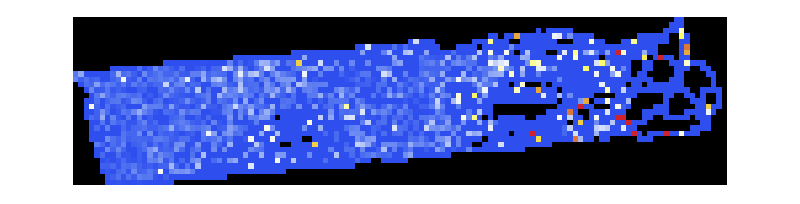

```mathematica
Row[{Show[{
metadataGraphic,Graphics[Raster[Map[If[#===Indeterminate,{0,0,0,0},Append[List@@ColorData["TemperatureMap"][#*10],0.8]]&,Transpose[Quiet[mergingArray/allCoordinatesArray]],{2}],Transpose[RegionBounds[paddockRegion]]]]
},ImageSize->800],BarLegend[{"TemperatureMap",{0,0.1}},LegendLabel->"merging event density"]}]
```

#### Regression of distance vs splitting proportion

Plot the event density as a function of distance to closest food or water

```mathematica
splittingArray=BinCounts[splittingCoordinates,{580401,586573,50},{6.562693*^6,6.564282*^6,50}];
```

Filter out squares with sparse data

```mathematica
minNumberAllCoordinatesArray=MapAt[If[#<50,Indeterminate,#]&,allCoordinatesArray,{All,All}];
```

```mathematica
splittingProportionArray =Quiet[ splittingArray/minNumberAllCoordinatesArray];
```

Define the square and their distance to the nearest food or water source

```mathematica
pointsOfInterest=Join[{water},feeding]
```

{{580661,6563573},{581448,6563715},{581450,6563434},{581358,6563183},{581175,6562960},{580935,6562820},{583822,6563068},{583848,6563266},{583860,6563462},{583860,6563657},{583851,6563852}}

```mathematica
positionArray = Table[{x,y},{x,580401+25,586573-25,50},{y,6.562693*^6+25,6.564282*^6-25,50}];
```

```mathematica
distanceArray=MapAt[EuclideanDistance[Catenate[Nearest[pointsOfInterest,#,DistanceFunction->EuclideanDistance]],#]&,positionArray,{All,All}];
```

```mathematica
splittingVsDistance=DeleteCases[Thread[{Flatten[distanceArray],Flatten[splittingProportionArray]}],{_,Indeterminate}];
```

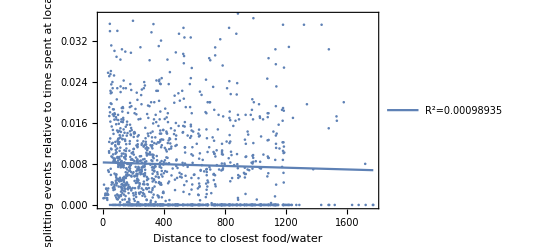

```mathematica
RegressionListPlot[splittingVsDistance,Frame->True,FrameLabel->{Style["Distance to closest food/water",Medium],Style["splitting events relative to time spent at location",Medium]},"DisplayRSquared"->True]
```

#### Number of times entering the spot

```mathematica
BinCounts[{580401,586573,50},{6.562693*^6,6.564282*^6,50}]
```

```mathematica
allCoordinatesMembersTime ={Mean[rawCoordinates[[#[[1]],#[[2]]]]],#[[1]],#[[2]]}&/@VertexList[fullGraph30Sticky50];
```

```mathematica
groupPaths=Catenate[Function[g,Split[g,(#2[[3]]-#1[[3]])===1&][[All,All,1]]]/@GatherBy[allCoordinatesMembersTime,Sort[#[[2]]]&]];
```

```mathematica
groupPathsNoDuplicates=Function[g,Split[Floor[{#[[1]]-580401,#[[2]]-6.562693*^6}&/@g,50]/50+1][[All,1]]]/@groupPaths;
```

```mathematica
groupPathsNoDuplicates=Function[g,Split[{#[[1]]+580401,#[[2]]+6.562693*^6}&/@Floor[{#[[1]]-580401,#[[2]]-6.562693*^6}&/@g,50]+1][[All,1]]]/@groupPaths;
```

```mathematica
noDuplicatesArray=BinCounts[Catenate[groupPathsNoDuplicates],{580401,586573,50},{6.562693*^6,6.564282*^6,50}];
```

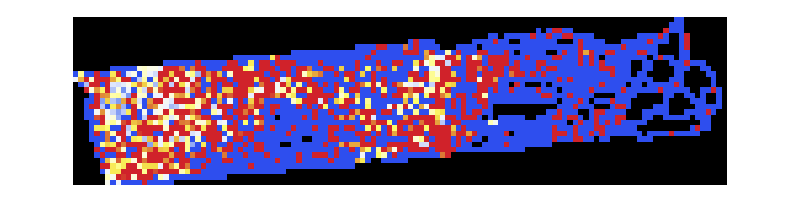

```mathematica
Row[{Show[{
metadataGraphic,Graphics[Raster[Map[If[#===Indeterminate,{0,0,0,0},Append[List@@ColorData["TemperatureMap"][#*10],0.8]]&,Transpose[Quiet[splittingArray/noDuplicatesArray]],{2}],Transpose[RegionBounds[paddockRegion]]]]
},ImageSize->800],BarLegend[{"TemperatureMap",{0,0.1}},LegendLabel->"Splitting event density"]}]
```

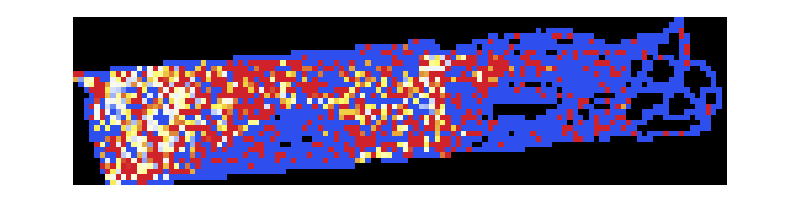

```mathematica
Row[{Show[{
metadataGraphic,Graphics[Raster[Map[If[#===Indeterminate,{0,0,0,0},Append[List@@ColorData["TemperatureMap"][#*10],0.8]]&,Transpose[Quiet[mergingArray/noDuplicatesArray]],{2}],Transpose[RegionBounds[paddockRegion]]]]
},ImageSize->800],BarLegend[{"TemperatureMap",{0,0.1}},LegendLabel->"Merging event density"]}]
```

#### Regression with number of times entering the spot

Repeat with entering locations rather than absolute frequency of visits

```mathematica
minNumberNoDuplicatesArray=MapAt[If[#<25,Indeterminate,#]&,noDuplicatesArray,{All,All}];
```

```mathematica
noDuplicatesSplittingProportionArray =Quiet[ splittingArray/minNumberNoDuplicatesArray];
```

```mathematica
noDuplicatesSplittingVsDistance=DeleteCases[Thread[{Flatten[distanceArray],Flatten[noDuplicatesSplittingProportionArray]}],{_,Indeterminate}];
```

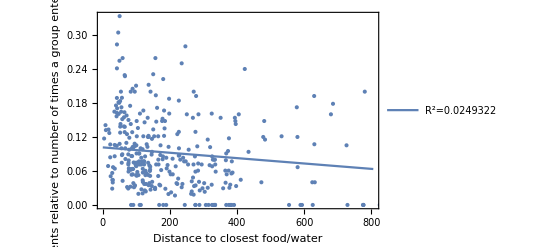

```mathematica
RegressionListPlot[noDuplicatesSplittingVsDistance,Frame->True,FrameLabel->{Style["Distance to closest food/water",Medium],Style["splitting events relative to \n number of times a group entered the location",Medium]},"DisplayRSquared"->True]
```

#### Regression of distance vs merging proportion

```mathematica
mergingArray=BinCounts[mergingCoordinates,{580401,586573,50},{6.562693*^6,6.564282*^6,50}];
```

```mathematica
mergingProportionArray =Quiet[ mergingArray/minNumberAllCoordinatesArray];
```

```mathematica
noDuplicatesMergingProportionArray=Quiet[ mergingArray/minNumberNoDuplicatesArray];
```

```mathematica
mergingVsDistance=DeleteCases[Thread[{Flatten[distanceArray],Flatten[mergingProportionArray]}],{_,Indeterminate}];
```

```mathematica
noDuplicatesMergingVsDistance=DeleteCases[Thread[{Flatten[distanceArray],Flatten[noDuplicatesMergingProportionArray]}],{_,Indeterminate}];
```

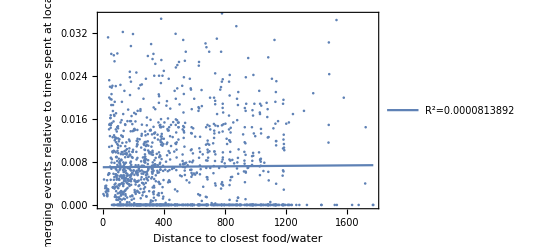

```mathematica
RegressionListPlot[mergingVsDistance,Frame->True,FrameLabel->{Style["Distance to closest food/water",Medium],Style["merging events relative to time spent at location",Medium]},"DisplayRSquared"->True]
```

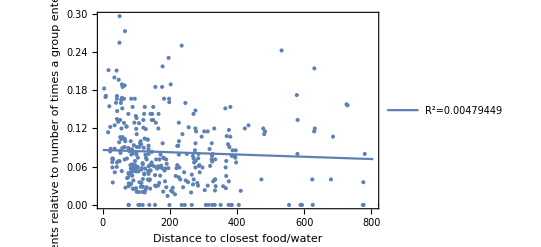

```mathematica
ResourceFunction["RegressionListPlot"][noDuplicatesMergingVsDistance,Frame->True,FrameLabel->{Style["Distance to closest food/water",Medium],Style["merging events relative to \n number of times a group entered the location",Medium]},"DisplayRSquared"->True]
```

### Time

#### Merging

Visualize the merging events in time

```mathematica
timePoints=rawTs[[2;;]][[mergingEvents[[All,2]],2]];
```

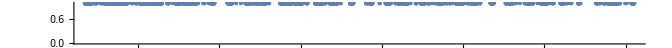

```mathematica
NumberLinePlot[timePoints]
```

```mathematica
dateObjectTimePoints=FromUnixTime[#,TimeZone->"Australia/Broken_Hill"]&/@timePoints;
```

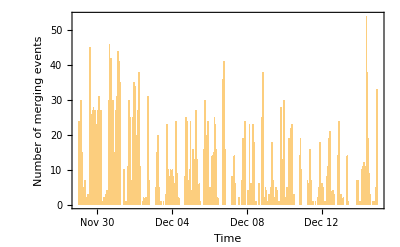

```mathematica
DateHistogram[dateObjectTimePoints,Quantity[1,"Hours"], Frame->True,FrameLabel->{"Time","Number of merging events"}]
```

Split by the hour of the day in which the events happen

```mathematica
hoursTimePoints=DateValue[#,"Hour"]&/@dateObjectTimePoints;
```

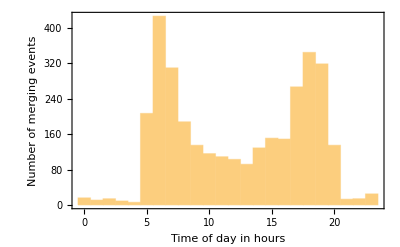

```mathematica
Histogram[hoursTimePoints, Frame->True,FrameLabel->{"Time of day in hours","Number of merging events"}]
```

#### Splitting

Repeat for splitting events

```mathematica
splittingTimePoints=rawTs[[2;;]][[splittingEvents[[All,2]],2]];
```

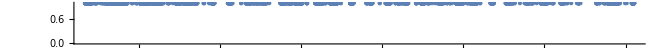

```mathematica
NumberLinePlot[splittingTimePoints]
```

```mathematica
splittingDateObjectTimePoints=FromUnixTime[#,TimeZone->"Australia/Broken_Hill"]&/@splittingTimePoints;
```

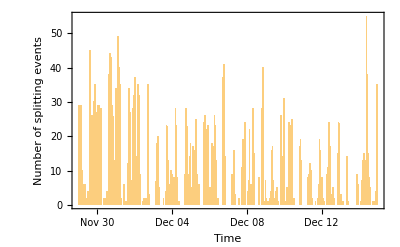

```mathematica
DateHistogram[splittingDateObjectTimePoints,Quantity[1,"Hours"], Frame->True,FrameLabel->{"Time","Number of splitting events"}]
```

Find the time of the day pattern

```mathematica
splittingHoursTimePoints=DateValue[#,"Hour"]&/@splittingDateObjectTimePoints;
```

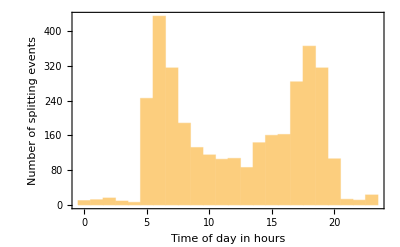

```mathematica
Histogram[splittingHoursTimePoints, Frame->True,FrameLabel->{"Time of day in hours","Number of splitting events"}]
```

#### Combined

Put time splitting and merging on the same plot

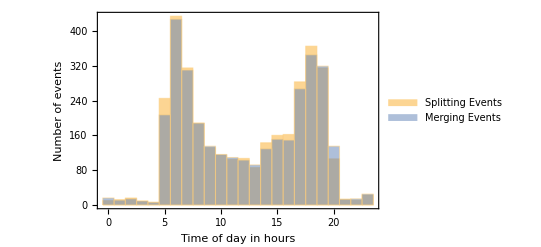

```mathematica
Histogram[{splittingHoursTimePoints,hoursTimePoints}, Frame->True,FrameLabel->{"Time of day in hours","Number of events"},ChartLegends->{"Splitting Events","Merging Events"}]
```

### Density over time

Define the network density as the number of actual edges over the possible ones

```mathematica
edgeDensityStickyDBSCAN[data_,{r1_,r2_},{tmin_,tmax_},rawCoordinates_]:=
Module[{cons,allEdges},
cons=Transpose[Catenate[Map[determineConnections[#,{r1,r2}]&,data[[All,All,tmin;;tmax]],{2}]]];
allEdges=UndirectedEdge@@@Catenate[MapIndexed[{#2[[1]],Total[#2]}&,data,{2}]];

MapIndexed[
With[{members=Flatten[Position[rawCoordinates[[All,tmin-1+First[#2]]],{__?NumericQ},{1},Heads->False]]},
Length[Select[Pick[allEdges,#1,True],FreeQ[Alternatives@@Complement[Range[Length[data]],members]]]]/Binomial[Length[members],2]//N]&,cons]]
```

```mathematica
allEdgeDensity =edgeDensityStickyDBSCAN[allPairData,{30,50},{1,210351},rawCoordinates];
```

```mathematica
allEdgeDensityTime=Transpose[{FromUnixTime[#,TimeZone->"Australia/Broken_Hill"]&/@rawTs[[2;;,2]],allEdgeDensity}];
```

Visualize the density over the study period

```mathematica
DateListPlot[allEdgeDensityTime,Frame->True,FrameLabel->{Style["date",Medium],Style["Network Density",Medium]},Joined->False]
```

-Graphics-

Split by minute and plot the average over the course of a day

```mathematica
byMin=GroupBy[allEdgeDensityTime,DateValue[#[[1]],{"Hour","Minute"}]&];
```

```mathematica
byMinMean=Values[{With[{n=DateValue[#[[1,1]],{"Hour","Minute"}]},n[[1]]+n[[2]]/10//N],Mean[#[[All,2]]]}&/@byMin];
```

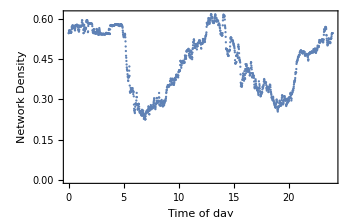

```mathematica
ListPlot[byMinMean, Frame->True,FrameLabel->{Style["Time of day",Medium],Style["Network Density",Medium]}]
```

## Personality data analysis

### Personality Data Repeatability & Distribution

#### Distribution of FID

Import and explore the personality dataset for FID

```mathematica
rawIDs2=Import["/Users/katjad/Documents/Github/SheepCapstone/ids.csv","Numeric"->False];
```

```mathematica
indexToEartag2=AssociationThread[Range[51],rawIDs2[[2;;,2]]];
```

```mathematica
eartagsToFID=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/IDmatching/eartagsToFID.mx"];
```

```mathematica
indexToFID=indexToEartag2/.eartagsToFID;
```

```mathematica
indexToMeanFID=MapAt[Mean,indexToFID,All]/.Mean["NA"]-> "NA";
```

Get the mean personality in each group

```mathematica
personalityHerds=DBSCAN30Sticky50LonelySheep/.indexToMeanFID/."NA"-> Missing[];
```

```mathematica
averagePersonality=Mean/@DeleteCases[DeleteCases[Catenate[personalityHerds[[All,1;;-2]]],Missing[],2],{}];
```

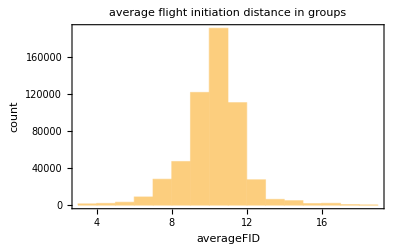

```mathematica
Histogram[averagePersonality,{1},Frame-> True,FrameLabel-> {"averageFID","count"},PlotLabel-> "average flight initiation distance in groups"]
```

```mathematica
splitDBSCAN=BlockMap[DBSCAN30Sticky50LonelySheep[[#[[1]]+1;;#[[2]]]]&,splitSequences,2,1];
```

```mathematica
splitPersonalityHerds=splitDBSCAN/.indexToMeanFID/."NA"-> Missing[];
```

```mathematica
splitAveragePersonality=(Mean/@DeleteCases[DeleteCases[Catenate[#[[All,1;;-2]]],Missing[],2],{}])&/@splitPersonalityHerds;
```

Test for similarity between repetitions

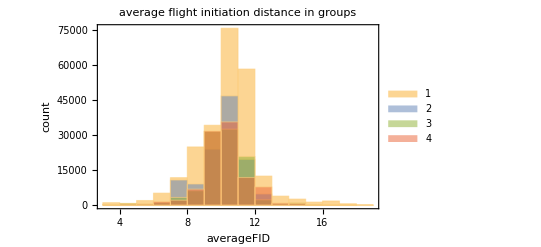

```mathematica
Histogram[splitAveragePersonality,{1},Frame-> True,ChartLegends->Automatic,FrameLabel-> {"averageFID","count"},PlotLabel-> "average flight initiation distance in groups"]
```

#### Distribution of Exploration Tendency

Repeat for Exploration Tendency

```mathematica
explorationRaw=Import["/Users/katjad/Documents/Github/SheepCapstone/buckets.csv","Numeric"->False];
```

```mathematica
flagToET=#[[2]]-> Length[DeleteCases[#[[9;;71-LengthWhile[Reverse[#],Function[x,x==="NA"]]]],"NA"]]/3&/@explorationRaw[[2;;]];
```

```mathematica
eartagToFlags=KeyMap[ToExpression,Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/IDmatching/earflags.mx"]];
```

```mathematica
indexToEartag=AssociationThread[Range[51],rawIDs[[2;;,2]]];
```

```mathematica
flagtoMeanET=KeyMap[ToExpression,KeySort[Merge[flagToET,N[Mean[#]]&]]];
```

```mathematica
indexToFlag=Map[ToExpression,indexToEartag/.eartagToFlags];
```

```mathematica
indexToMeanET=indexToFlag/.flagtoMeanET;
```

```mathematica
flagToListET=KeySort[Merge[flagToET,#&]];
```

Visualize variation in exploration tendency

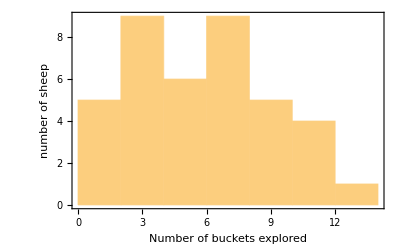

```mathematica
Histogram[Values[indexToMeanET],Frame->True,FrameLabel-> {"Number of buckets explored","number of sheep"}]
```

### Time Alone

#### FID x Time Alone

Extract the time each sheep spent in a group of size 1 (aka. alone), normalizing for available data

```mathematica
availableData=Length[DeleteCases[rawCoordinates[[#]],{Missing[],Missing[]}]]&/@Range[51];
```

```mathematica
splitAvailableData=Table[Length[DeleteCases[splitRawCoordinates[[x,#]],{Missing[],Missing[]}]],{x,1,4}]&/@Range[51];
```

```mathematica
groupStability30Sticky50=GroupBy[Catenate[MapIndexed[#1->First[#2]&,DBSCAN30Sticky50LonelySheep,{2}]],First->Last,Join];
```

```mathematica
groupToTimeAlone=Length/@KeySelect[SortBy[groupStability30Sticky50,Length],Length[#]==1&][[ ;;51]];
```

```mathematica
indexToTimeAlone=Association[#->(groupToTimeAlone[{#}]/availableData[[#]])&/@Range[51]];
```

```mathematica
FIDTimeAlone=DeleteCases[Table[{indexToMeanFID[x],indexToTimeAlone[x]},{x,51}],{"NA",_}];
```

Find the regression

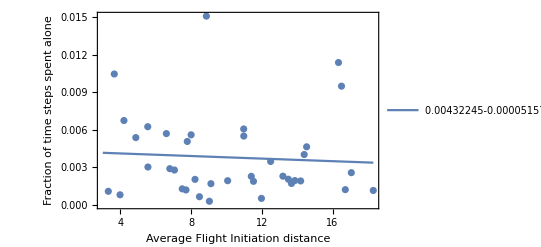

```mathematica
RegressionListPlot[Delete[FIDTimeAlone,17],Frame-> True,FrameLabel-> {Style["Average Flight Initiation distance",Medium],Style["Fraction of time steps spent alone",Medium]},"DisplayEquation"->True,"DisplayRSquared"-> True,PlotRange->All]
```

#### FID x Split Time Alone

Split the dataset into the three components and repeat

```mathematica
splitGroupStability30Sticky50=GroupBy[Catenate[MapIndexed[#1->First[#2]&,#,{2}]],First->Last,Join]&/@splitDBSCAN;
```

```mathematica
splitGroupToTimeAlone=(Length/@KeySelect[SortBy[#,Length],Function[x,Length[x]==1]])&/@splitGroupStability30Sticky50;
```

```mathematica
(*splitIndexToTimeAlone=Map[Function[x,Association[#-> If[IntegerQ[x[{#}]],x[{#}],0]&/@Range[51]]],splitGroupToTimeAlone];*)
```

```mathematica
splitIndexToTimeAlone=MapIndexed[Function[{x,i},Association[#-> If[splitAvailableData[[#,i[[1]]]]>1000&&IntegerQ[x[{#}]]&&#=!=17,x[{#}]/splitAvailableData[[#,i[[1]]]],0]&/@Range[51]]],splitGroupToTimeAlone];
```

```mathematica
SplitFIDTimeAlone=DeleteCases[Table[{indexToMeanFID[x],#[x]},{x,51}],{"NA",_}]&/@splitIndexToTimeAlone;
```

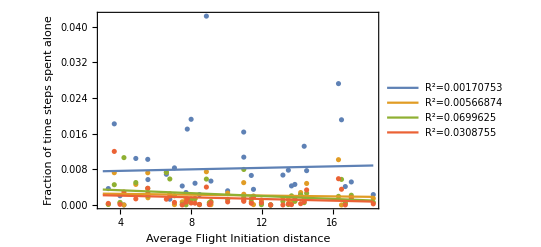

```mathematica
RegressionListPlot[Delete[#,17]&/@SplitFIDTimeAlone,Frame-> True,FrameLabel-> {Style["Average Flight Initiation distance",Medium],Style["Fraction of time steps spent alone",Medium]},"DisplayRSquared"-> True,PlotRange->All]
```

```mathematica
SplitIndexTimeAlone=Catenate[DeleteCases[Table[{x,#[x]},{x,51}],{"NA",_}]&/@splitIndexToTimeAlone];
```

```mathematica
Export["/Users/katjad/Documents/Github/SheepCapstone/indexAndTimeAlone.csv",SplitIndexTimeAlone];
```

#### ET x Time Alone

```mathematica
ETTimeAlone=DeleteCases[Table[{indexToMeanET[x],indexToTimeAlone[x]},{x,51}],{NA,_}];
```

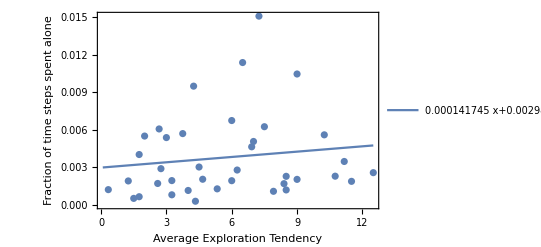

```mathematica
RegressionListPlot[Delete[ETTimeAlone,17],Frame-> True,FrameLabel-> {Style["Average Exploration Tendency",Medium],Style["Fraction of time steps spent alone",Medium]},"DisplayEquation"->True,"DisplayRSquared"-> True,PlotRange->All]
```

#### ET x Split Time Alone

```mathematica
SplitETTimeAlone=DeleteCases[Table[{indexToMeanET[x],#[x]},{x,51}],{NA,_}]&/@splitIndexToTimeAlone;
```

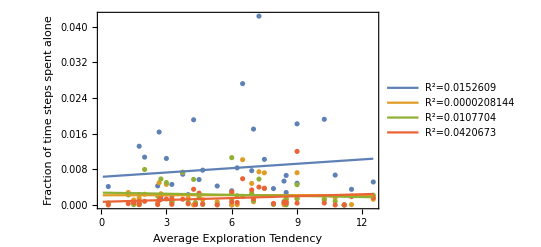

```mathematica
RegressionListPlot[Delete[#,17]&/@SplitETTimeAlone,Frame-> True,FrameLabel-> {Style["Average Exploration Tendency",Medium],Style["Fraction of time steps spent alone",Medium]},"DisplayRSquared"-> True,PlotRange->All]
```

### Average Group Size

#### Data Prep full dataset

```mathematica
indexToGroupLengths30Sticky50=Merge[GeneralUtilities`MonitoredMap[Function[ts,Catenate[Function[g,Function[s,s->Length[g]]/@g]/@ts]],DBSCAN30Sticky50LonelySheep],Identity];
```

```mathematica
(*Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/GroupStability/indexToGroupLengths30Sticky50.mx",indexToGroupLengths30Sticky50];*)
```

```mathematica
indexToGroupLengths30Sticky50=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/GroupStability/indexToGroupLengths30Sticky50.mx"];
```

```mathematica
indexToMeanGroupLength30Sticky50=Association[#->Mean[indexToGroupLengths30Sticky50[#]]&/@Range[51]];
```

```mathematica
indexToMedianGroupLength30Sticky50=Association[#->Median[indexToGroupLengths30Sticky50[#]]&/@Range[51]];
```

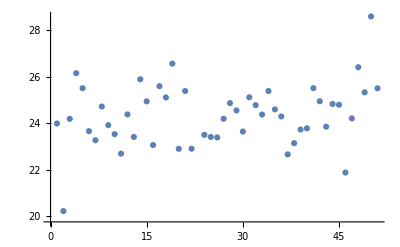

```mathematica
ListPlot[Delete[indexToMeanGroupLength30Sticky50,23],PlotRange->All]
```

#### Data prep split dataset

```mathematica
splitIndexToGroupLengths30Sticky50=Map[Merge[GeneralUtilities`MonitoredMap[Function[ts,Catenate[Function[g,Function[s,s->Length[g]]/@g]/@ts]],#],Identity]&,splitDBSCAN];
```

```mathematica
(*Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/GroupStability/splitIndexToGroupLengths30Sticky50.mx",splitIndexToGroupLengths30Sticky50];*)
```

```mathematica
splitIndexToGroupLengths30Sticky50=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/GroupStability/splitIndexToGroupLengths30Sticky50.mx"];
```

```mathematica
splitIndexToMeanGroupLengths30Sticky50=Map[Mean,splitIndexToGroupLengths30Sticky50,{2}]//N;
```

```mathematica
splitIndexToMeanGroupLengths30Sticky50=Function[ti,Association[DeleteCases[Function[in,If[KeyExistsQ[ti,in],in->Median[ti[in]]]]/@Range[51],Null]]]/@splitIndexToGroupLengths30Sticky50;
```

Export for ICC calculation

```mathematica
splitIndexMeanGroupLengthCSV=Catenate[Map[Function[rep,If[KeyExistsQ[rep,#],{#,rep[#]},Nothing]&/@Range[51]],splitIndexToMeanGroupLengths30Sticky50]];
```

```mathematica
Export["/Users/katjad/Documents/Github/SheepCapstone/splitIndexMeanGroupLengths.csv",splitIndexMeanGroupLengthCSV];
```

#### FID x Average Group Size

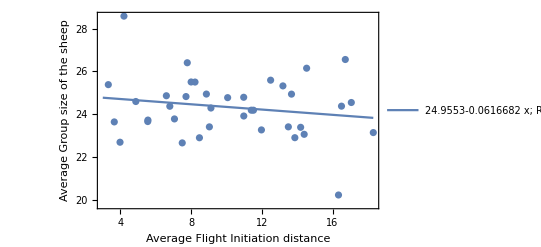

```mathematica
RegressionListPlot[Delete[DeleteCases[Table[{indexToMeanFID[FID],indexToMeanGroupLength30Sticky50[FID]//N},{FID,51}],{"NA",_}],17],Frame->True,FrameLabel->{Style["Average Flight Initiation distance",Medium],Style["Average Group size of the sheep",Medium]},"DisplayEquation"->True,"DisplayRSquared"->True,PlotRange->All]
```

#### FID x Split Average Group Size

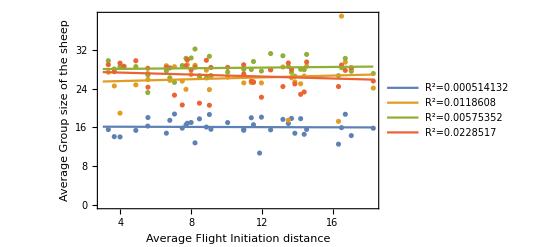

```mathematica
RegressionListPlot[DeleteCases[Table[{indexToMeanFID[FID],#[FID]//N},{FID,51}],{"NA",_}|{_,_Missing}]&/@splitIndexToMeanGroupLengths30Sticky50,Frame->True,FrameLabel->{Style["Average Flight Initiation distance",Medium],Style["Average Group size of the sheep",Medium]},"DisplayRSquared"->True,PlotRange->All]
```

#### ET x Average Group Size

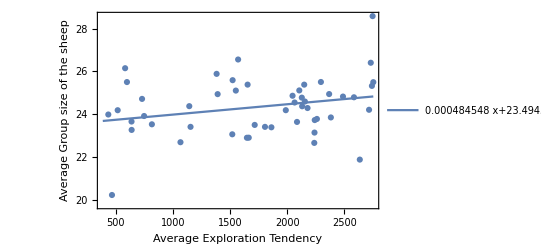

```mathematica
RegressionListPlot[Delete[DeleteCases[Table[{indexToMeanET[x],indexToMeanGroupLength30Sticky50[x]//N},{x,51}],{"NA",_}],23],Frame->True,FrameLabel->{Style["Average Exploration Tendency",Medium],Style["Average Group size of the sheep",Medium]},"DisplayEquation"->True,"DisplayRSquared"->True,PlotRange->All]
```

#### ET x Split Average Group Size

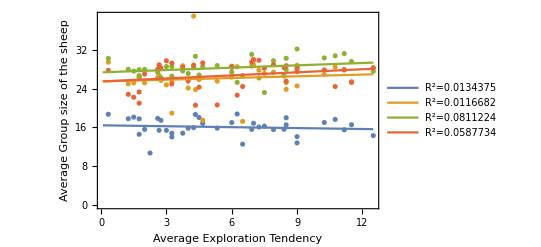

```mathematica
RegressionListPlot[DeleteCases[Table[{indexToMeanET[FID],#[FID]//N},{FID,51}],{NA,_}|{_,_Missing}]&/@splitIndexToMeanGroupLengths30Sticky50,Frame->True,FrameLabel->{Style["Average Exploration Tendency",Medium],Style["Average Group size of the sheep",Medium]},"DisplayRSquared"->True,PlotRange->All]
```

### Centrality in Group

#### Data Prep full dataset

Find the distance to the center of the group relative to all other group members in groups of five or more

Find euclidean distance to center for each of the sheep in the list and return association

```mathematica
findEuclideanDistanceCenter[herd_,timestep_]:=Association[
With[{center=Mean[rawCoordinates[[herd,timestep]]]},#->EuclideanDistance[rawCoordinates[[#,timestep]],center]&/@herd]]
```

```mathematica
rawEuclideanDistances=MapIndexed[Function[group,findEuclideanDistanceCenter[group,n=#2[[1]]]]/@#1&,DBSCAN30Sticky50LonelySheep];
```

```mathematica
indexToEuclideanDistance=Map[Mean,AssociationMap[DeleteMissing[Catenate[rawEuclideanDistances[[All,All,Key[#]]]]]&,Range[51]]];
```

```mathematica
indexToEuclideanDistance
```

<|1→13.1058,2→13.1199,3→11.709,4→13.0976,5→12.186,6→13.5965,7→10.9256,8→11.5567,9→12.6579,10→13.2765,11→12.6816,12→12.7403,13→11.3784,14→12.6407,15→11.4161,16→13.3304,17→12.8929,18→12.8933,19→12.0179,20→10.493,21→11.2854,22→11.7779,23→9.7933,24→12.0068,25→10.405,26→12.0779,27→10.9583,28→12.7034,29→12.6428,30→13.11,31→11.6859,32→12.1316,33→12.4398,34→12.0846,35→13.5187,36→10.9482,37→10.4908,38→10.8904,39→11.8685,40→12.2106,41→12.4226,42→12.2571,43→11.2791,44→12.0143,45→12.992,46→13.3885,47→12.8848,48→12.6209,49→12.3868,50→13.9745,51→11.8087|>

```mathematica
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/Centrality/indexToEuclideanDistance.mx",indexToEuclideanDistance];
```

#### Data Prep split Dataset

```mathematica
splitRawEuclideanDistances=BlockMap[rawEuclideanDistances[[#[[1]]+1;;#[[2]]]]&,splitSequences,2,1];
```

```mathematica
splitIndexToEuclideanDistance=Map[Mean,Function[interval,AssociationMap[DeleteMissing[Catenate[interval[[All,All,Key[#]]]]]&,Range[51]]]/@splitRawEuclideanDistances,{2}];
```

```mathematica
splitIndexCentralityCSV=DeleteCases[Catenate[Map[Function[rep,If[KeyExistsQ[rep,#],{#,rep[#]},Nothing]&/@Range[51]],splitIndexToEuclideanDistance]],{_,Mean[{}]}];
```

```mathematica
Export["/Users/katjad/Documents/Github/SheepCapstone/splitIndexCentralityCSV.csv",splitIndexCentralityCSV];
```

#### FID x Centrality

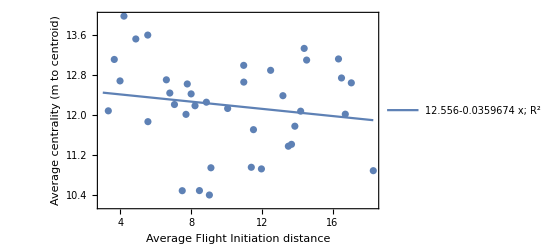

```mathematica
RegressionListPlot[Delete[DeleteCases[Table[{indexToMeanFID[FID],indexToEuclideanDistance[FID]//N},{FID,51}],{"NA",_}|{_,Mean[{}]}],17],Frame->True,FrameLabel->{Style["Average Flight Initiation distance",Medium],Style["Average centrality (m to centroid)",Medium]},"DisplayEquation"->True,"DisplayRSquared"->True,PlotRange->All]
```

#### FID x split centrality

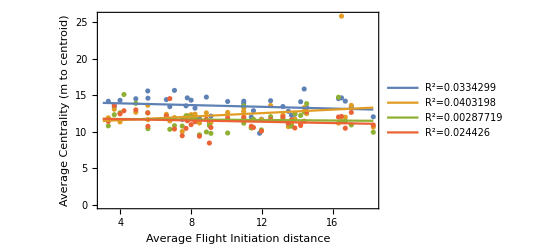

```mathematica
RegressionListPlot[DeleteCases[Table[{indexToMeanFID[FID],#[FID]//N},{FID,51}],{"NA",_}|{_,Mean[{}]}]&/@splitIndexToEuclideanDistance,Frame->True,FrameLabel->{Style["Average Flight Initiation distance",Medium],Style["Average Centrality (m to centroid)",Medium]},"DisplayRSquared"->True,PlotRange->All]
```

#### ET x Centrality

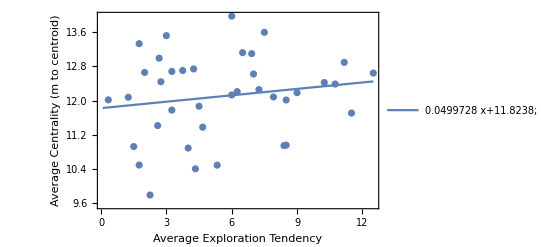

```mathematica
RegressionListPlot[Delete[DeleteCases[Table[{indexToMeanET[x],indexToEuclideanDistance[x]//N},{x,51}],{NA,_}],23],Frame->True,FrameLabel->{Style["Average Exploration Tendency",Medium],Style["Average Centrality (m to centroid)",Medium]},"DisplayEquation"->True,"DisplayRSquared"->True,PlotRange->All]
```

#### ET x splitCentrality

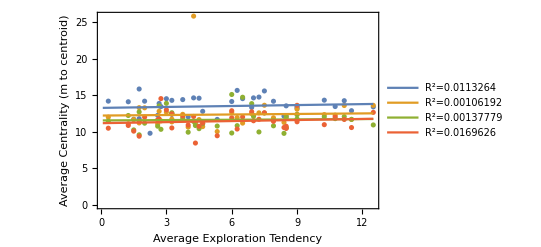

```mathematica
RegressionListPlot[DeleteCases[Table[{indexToMeanET[FID],#[FID]//N},{FID,51}],{NA,_}|{_,Mean[{}]}]&/@splitIndexToEuclideanDistance,Frame->True,FrameLabel->{Style["Average Exploration Tendency",Medium],Style["Average Centrality (m to centroid)",Medium]},"DisplayRSquared"->True,PlotRange->All]
```

## Code that didn’t make it into the final version for #designthinking

### Dimension Reduction (for y-coordinates on some plots)

To represent the coordinate of each sheep as a single value, I use a dimension-reduction algorithm

```mathematica
trainingData=RandomSample[DeleteMissing[Catenate[rawCoordinates],1,2],100000];
```

```mathematica
linearDR=DimensionReduction[trainingData,1,Method-> "Linear"];
```

```mathematica
linearDimensionReductionData=linearDR[rawCoordinates[[#]]]&/@Range[51];
```

```mathematica
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/DimensionReduction/linearDimensionReduction.mx",linearDimensionReductionData]
```

/Users/katjad/Documents/Github/SheepCapstone/MXs/DimensionReduction/linearDimensionReduction.mx

```mathematica
linearDimensionReductionData=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/DimensionReduction/linearDimensionReduction.mx"];
```

```mathematica
Dimensions[linearDimensionReductionData]
```

{51,210351,1}

```mathematica
principalComponentDR = DimensionReduction[trainingData,1,Method-> "PrincipalComponentsAnalysis"];
```

```mathematica
latentSemanticAnalysisDR = DimensionReduction[RandomSample[trainingData,100000],1,Method-> "AutoEncoder"];
```

```mathematica
latentSemanticAnalysisDR
```

DimensionReducerFunction[…]

### Sticky DBSCAN (early, non-symmetric version)

```mathematica
(*
Output: clusters for the sheep as traditional DBSCAN but with sheep tending to "stick" to the group they are already with. If r1=r2, equivalent to DBSCAN
Inputs: 
- pts (locations of the sheep, 2D, list of list)
- r1 (smaller of the two radii, sheep are considered together)
-r2(larger of the two radii, sheep are considered together only if they were in the same group in the last time step)
- k (minimum number of neighbors(including oneself) to be considered a core point)
- indexPrevClusters (Association from each cluster to the neighbors in the previous cluster)*)
dbscanSticky[pts_,{r1_,r2_},k_,indexPrevClusters_]:=
Module[{indexPts,nf,pointNeighbors,coreIndices,clusterCores,coreClusters,noncoreIndices,clusterNoncores},
(*Turn points into association with the correct index, delete missing points*)
indexPts=DeleteMissing[AssociationThread[Range[Length[pts]],pts],1,2];
(*Define nearest function*)
nf=Nearest[indexPts];
(*For each point, find its neighbors, considering whether they were neighbors in the previous time step or not*)
pointNeighbors=
Association[MapThread[
#2->With[{prevNeighbors=indexPrevClusters[#2]},
Select[#1,Function[n,
With[{d=EuclideanDistance[indexPts[#2],indexPts[n]]},
If[MemberQ[prevNeighbors,n],d≤r2,d≤r1]
]
]]
]&,
{nf[Values[indexPts],{All,r2}][[All,2;;]],Keys[indexPts]}
]];
(*Find all core points*)
coreIndices=Position[pointNeighbors,_?(Length[#]+1≥k&),{1},Heads->False][[All,1,1]];
(*Form the clusters just from the core points*)
clusterCores=
ConnectedComponents[
Catenate[MapThread[
Thread[#1->#2]&,{
coreIndices,
Select[MemberQ[coreIndices,#]&]/@Lookup[pointNeighbors,coreIndices]
}]]
];
coreClusters=Association[Catenate[MapIndexed[Thread[#1->First[#2]]&,clusterCores]]];
(*Consider all points that are not cores*)
noncoreIndices=Complement[Keys[indexPts],coreIndices];
(*if they could be in more than one cluster, chose randomly*)
clusterNoncores=Merge[Lookup[coreClusters,pointNeighbors[#],Nothing]->#&/@noncoreIndices,Identity];
KeyValueMap[
With[{c=RandomChoice[#1]},clusterCores[[c]]=Join[clusterCores[[c]],#2]]&,
KeyDrop[clusterNoncores,Key[{}]]
];
(*Return the full set of clusters, add an empty list if none of the sheep are alone*)
Append[clusterCores,Lookup[clusterNoncores,Key[{}],{}]]
]
```

```mathematica
fullDBScan[data_,{r1_,r2_},k_,{minTime_,maxTime_}]:=FoldPairList[With[{clustering=dbscanSticky[#2,{r1,r2},k,#1]},{clustering,Join[#1,Association[Catenate[Function[c,#->c&/@c]/@clustering]]]}]&,Association[#->{}&/@Range[Length[data]]],Transpose[data][[minTime;;maxTime]]]
```

```mathematica
DBSCAN30Sticky50 =fullDBScan[rawCoordinates,{30,50},2,{1,210351}];
```

```mathematica
DBSCAN3Sticky5 =fullDBScan[rawCoordinates,{3,5},2,{1,210351}];
```

```mathematica
DBSCAN30Sticky50LonelySheep=Join[Most[#],List/@Last[#]]&/@DBSCAN30Sticky50;
```

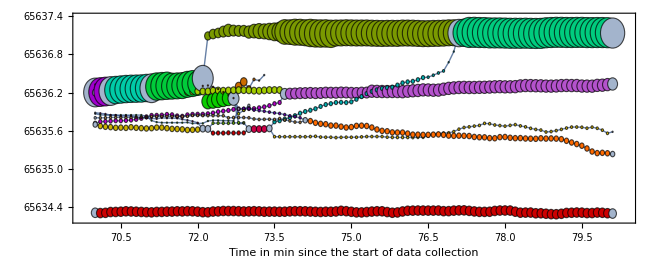

```mathematica
coloredGraph[graph30Sticky50,100]
```

## Cost-benefit of grouping

Cost-benefit function vs foraging alone

```mathematica
costBenefit[size_]:=100*PDF[NormalDistribution[8,5],size-1]
```

```mathematica
forageAlone[size_]:=costBenefit[1]
```

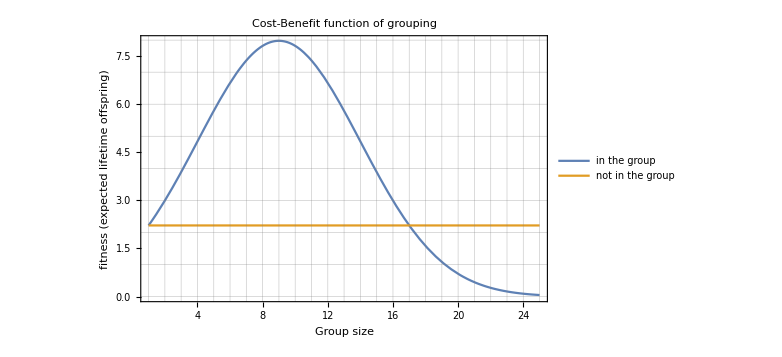

```mathematica
Plot[{costBenefit[x],forageAlone[x]},{x,1,25},Frame->True,PlotLabel->Style["Cost-Benefit function of grouping",Large],FrameLabel->{Style["Group size",Medium],Style["fitness \n(expected lifetime offspring)",Medium]},PlotLegends->Placed[LineLegend[{"in the group","not in the group"},LegendFunction->(Framed[#,Background->White]&)],{0.8,0.8}],GridLines->{Range[0,25],Range[0,8,1]}]
```

## Method developed for convenience

Since I will be running the regression repeatedly, I created a function (I also made this publicly available at https://resources.wolframcloud.com/FunctionRepository/resources/RegressionListPlot/ ).
The local definition will be used to make sure everything is reproducible in case I update the public facing version.

### RegressionListPlot

```mathematica
RegressionListPlot[d_,opts:OptionsPattern[]]:=
	Block[{data,x,listplot,listmin,listmax,degree,equations,rsquared},
		data=If[Depth[d]==2,
				{Table[{x,d[[x]]},{x,1,Length[d]}]},
				If[Depth[d]==3,
					{d},
					d]];
		degree=If[Depth[OptionValue["Degree"]]==1,
				Table[OptionValue["Degree"],Length[data]],
				OptionValue["Degree"]];
		equations=Fit[#[[1]],x^(#-1)&/@Range[#[[2]]+1],x]&/@Transpose[{data,degree}];
		rsquared=(Correlation@@Transpose[#])^2&/@data;
		listplot=ListPlot[data,Evaluate[Sequence@@FilterRules[{opts},Options[ListPlot]]]];
		{listmin,listmax}=AbsoluteOptions[listplot,PlotRange][[1,2,1]];
		Show[
			listplot,
			Plot[Evaluate[equations],
			{x,listmin,listmax},
			PlotLegends->If[TrueQ[OptionValue["DisplayEquation"]],
				If[TrueQ[OptionValue["DisplayRSquared"]],
					Row[{equations[[#]],StringTemplate["; \nR^2=``"][rsquared[[#]]]}]&/@Range[Length[equations]],
					equations],
				If[TrueQ[OptionValue["DisplayRSquared"]],
					StringTemplate["R^2=``"][rsquared[[#]]]&/@Range[Length[rsquared]],
					None]],
			Evaluate[Sequence@@FilterRules[{opts},Options[Plot]]]]]]
```

```mathematica
Options[RegressionListPlot]=Join[{"Degree"->1, "DisplayEquation"->False, "DisplayRSquared"->False},Normal@Merge[{Options[Plot],Options[ListPlot]},First]];
```

<|1|>
 |  |  |  |

## Group size distribution

### Overall

```mathematica
adjustedGroupSizes=Flatten[Table[Length[#],Length[#]]&/@Catenate[DBSCAN30Sticky50LonelySheep]];
```

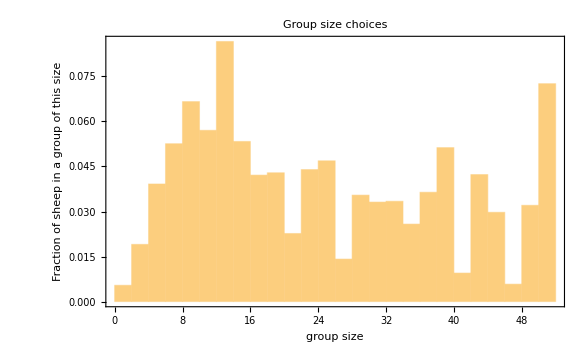

```mathematica
Histogram[adjustedGroupSizes,Automatic,"Probability",Frame->True,PlotLabel->Style["Group size choices",Large],FrameLabel->{Style["group size",Medium],Style["Fraction of sheep\nin a group of this size",Medium]}]
```

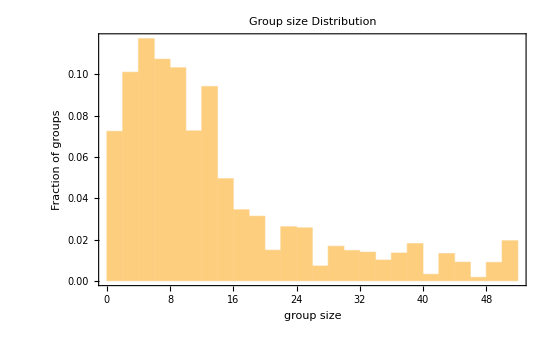

```mathematica
Histogram[Length/@Catenate[DBSCAN30Sticky50LonelySheep],Automatic,"Probability",PlotLabel->Style["Group size Distribution",Large],Frame->True,FrameLabel->{Style["group size",Medium],Style["Fraction of groups",Medium]}]
```

### Day vs Night

```mathematica
timedDBSCAN30Sticky50LonelySheep=Transpose[{DateValue[FromUnixTime[#,TimeZone->"Australia/Broken_Hill"]&/@rawTs[[2;;,2]],"Hour"],DBSCAN30Sticky50LonelySheep}];
```

```mathematica
timedDBSCAN30Sticky50LonelySheep[[1]]
```

{15,{{5,8,17,21,22,33,35,38,40,44,48}}}

#### From 10pm to 5am

```mathematica
night=Select[timedDBSCAN30Sticky50LonelySheep,(#[[1]]<5||#[[1]]>=22)&][[All,2]];
```

```mathematica
nightSizes=Flatten[Table[Length[#],Length[#]]&/@Catenate[night]];
```

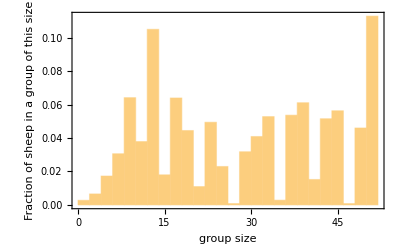

```mathematica
Histogram[nightSizes,Automatic,"Probability",Frame->True,FrameLabel->{"group size","Fraction of sheep\nin a group of this size"}]
```

#### From 5am to 12pm

```mathematica
morning=Select[timedDBSCAN30Sticky50LonelySheep,5<=#[[1]]<12&][[All,2]];
```

```mathematica
morningSizes=Flatten[Table[Length[#],Length[#]]&/@Catenate[morning]];
```

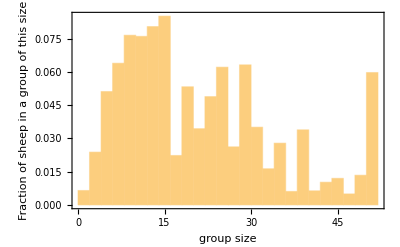

```mathematica
Histogram[morningSizes,Automatic,"Probability",Frame->True,FrameLabel->{"group size","Fraction of sheep\nin a group of this size"}]
```

#### Morning and Night

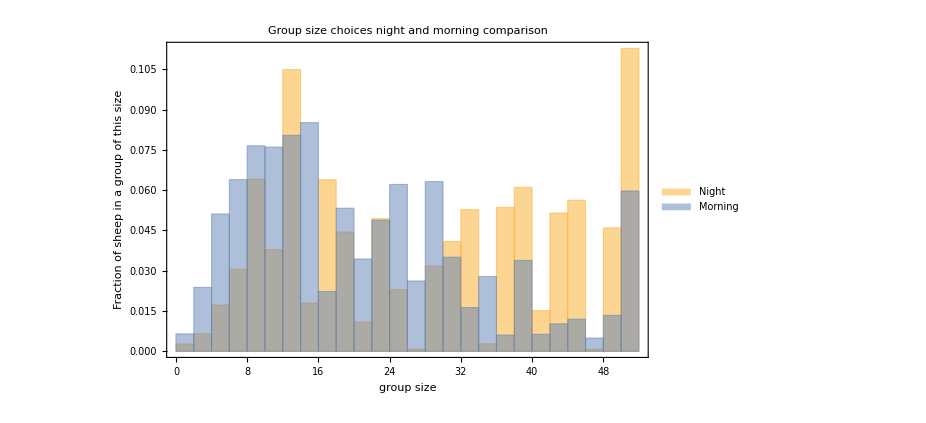

```mathematica
Histogram[{nightSizes,morningSizes},Automatic,"Probability",Frame->True,PlotLabel->Style["Group size choices night and morning comparison",Large],ChartLegends->Placed[SwatchLegend[{"Night","Morning"},LegendFunction->(Framed[#,Background->White]&)],{0.7,0.8}],FrameLabel->{Style["group size",Medium],Style["Fraction of sheep\nin a group of this size",Medium]}]
```